```mathematica
NormalizePart[s_]:=Sort[Map[Sort[#]&,s],#1[[1]]<#2[[1]]&]
```

```mathematica
VertexSetRotations[s_]:=Block[{range=Range[5],i,rep,result={}},
For[i=1,i≤5,i++,
rep=Table[i->range[[i]],{i,5}];
AppendTo[result,NormalizePart[s/.rep]];
range=RotateRight[range,1]
];
DeleteDuplicates[result]
]
```

```mathematica
allGraphs5[K3Key,"vertexsets"]
```

{{1},{2},{3},{4},{5}}

```mathematica
VertexSetRotations[allGraphs5[alfa1Key,"vertexsets"]]
```

{{{1,3},{2,4},{5}},{{1,3},{2,5},{4}},{{1,4},{2,5},{3}},{{1,4},{2},{3,5}},{{1},{2,4},{3,5}}}

```mathematica
Tally
```

Tally

```mathematica
MemberQ[VertexSetRotations[allGraphs5[alfa1Key,"vertexsets"]],allGraphs5[beta1Key,"vertexsets"]]
```

True

```mathematica
allGraphs5[beta1Key,"vertexsets"]
```

{{1,4},{2,5},{3}}

```mathematica
VertexSetRotations[allGraphs5[alfa1Key,"vertexsets"]]
```

{{{1,3},{2,4},{5}},{{1,3},{2,5},{4}},{{1,4},{2,5},{3}},{{1,4},{2},{3,5}},{{1},{2,4},{3,5}}}

```mathematica
Length[groups]
```

495

```mathematica
Length[allGraphs4AtomKeys]
```

15

```mathematica
Table[ShowGraph5Least[k],{k,{19683,6561,2187,729,243,81,27,9,3,1}}]
```

{-Graphics-1968321,-Graphics-656124,-Graphics-218724,-Graphics-72921,-Graphics-24321,-Graphics-8124,-Graphics-2724,-Graphics-921,-Graphics-324,-Graphics-121}

```mathematica
VertexSetRotations[allGraphs5[19683,"vertexsets"]]
```

{{{1},{2},{3},{4},{5}}}

```mathematica
RotatedGraphs[g_]:=Block[{range=VertexList[g],i,rep,result={}},
For[i=1,i≤Length[range],i++,
rep=Table[i->range[[i]],{i,Length[range]}];
AppendTo[result,Sort[Map[Sort,EdgeList[g]/.rep]]];
range=RotateRight[range,1]
];
DeleteDuplicates[result]
]
```

```mathematica
RotatedGraphs[allGraphs5[alfa1Key,"graph"]]
```

{{1<->2,1<->3,2<->3}}

```mathematica
SameBucket[k1_,k2_]:=Block[{
g1=allGraphs5[k1,"graph"],
g2=allGraphs5[k2,"graph"],
range,
i,
rep,
edges1,
result,
vertices=allGraphs5[k1,"vertexsets"]},
range=VertexList[g1];
If[VertexCount[g1]≠VertexCount[g2],Return[False]];
If[!IsomorphicGraphQ[g1,g2],Return[False]];
If[EdgeCount[g1]≠EdgeCount[g2],Return[False]];
For[i=1,i≤Length[range],i++,
rep=Table[i->range[[i]],{i,Length[range]}];
edges1=Sort[Map[Sort,EdgeList[g1]/.rep]];
If[edges1==EdgeList[g2],
If[Sort[Tally[Flatten[allGraphs5[k1,"matrix"]]]]!=Sort[Tally[Flatten[allGraphs5[k2,"matrix"]]]],
(*.Print[g1,g2,Sort[Tally[Flatten[allGraphs5[k1,"matrix"]]]],"     ",Sort[Tally[Flatten[allGraphs5[k2,"matrix"]]]]];*)
Return[False]
];
(*If[Sort[Map[Differences,allGraphs5[k1,"vertexsets"]]]!=Sort[Map[Differences,allGraphs5[k2,"vertexsets"]]],
(*Print[g1,g2,Sort[Map[Differences,allGraphs5[k1,"vertexsets"]]],"     ",Sort[Map[Differences,allGraphs5[k2,"vertexsets"]]]];*)
Return[False]
];*)
Return [True]
];
range=RotateRight[range,1]
];
Return[False]
]
```

```mathematica
groups=Gather[Keys[allGraphs5],
SameBucket[#1,#2]&];Length[groups]
```

269

```mathematica
groups=Gather[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#1,"graph"],allGraphs5[#2,"graph"]]
&&MemberQ[VertexSetRotations[allGraphs5[#1,"vertexsets"]],allGraphs5[#2,"vertexsets"]
&&MemberQ[RotatedGraphs[allGraphs5[#1,"graph"]],EdgeList[allGraphs5[#2,"graph"]]]]&];
```

```mathematica
Length[groups]
```

279

```mathematica
TableToBuckets[]:=Block[{result=Association[],i},
For[i=1,i≤Length[groups],i++,
Table[result[key]=i,{key,groups[[i]]}]
];
result
]
```

```mathematica
map=TableToBuckets[];Length[map]
```

1895

```mathematica
edges=DeleteDuplicates[Flatten[Table[
Table[
Table[
map[k]->map[c]
,{c,children}
]
,{children,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}]]]
```

{1→2,1→258,1→269,1→278,2→3,2→208,2→216,2→240,2→181,2→247,2→253,2→256,2→257,3→4,3→117,3→134,3→102,3→169,3→181,3→185,3→197,3→203,3→205,3→207,4→5,4→45,4→83,4→102,4→107,4→117,4→121,4→65,4→127,4→129,4→131,5→6,5→45,5→53,5→65,5→68,5→75,5→79,5→81,6→7,6→29,6→33,6→39,6→24,6→42,6→44,7→8,7→18,7→21,7→24,7→26,7→28,7→15,8→9,8→15,8→17,8→18,8→19,9→10,9→13,9→14,9→12,10→11,10→12,14→11,14→13,15→12,15→16,17→10,17→12,18→13,18→16,19→14,19→12,19→10,19→13,18→20,21→9,21→13,21→22,21→23,21→12,22→10,22→13,22→14,22→12,23→14,23→13,24→15,24→20,24→25,24→16,25→12,25→20,26→17,26→18,26→22,26→25,26→27,26→12,27→10,27→18,27→14,27→25,28→19,28→18,28→23,28→25,28→27,28→13,29→18,29→31,29→32,29→30,18→30,32→13,32→31,33→8,33→18,33→34,33→15,33→37,33→29,33→38,34→9,34→18,34→35,34→32,34→36,34→12,35→10,35→13,35→14,35→12,32→30,36→14,36→18,36→32,37→17,37→13,37→35,37→12,37→9,29→16,38→19,38→18,38→36,38→12,38→9,38→32,29→20,39→21,39→29,39→34,39→32,39→40,39→41,39→25,40→22,40→32,40→35,40→23,40→25,25→31,41→23,41→18,41→36,41→13,41→32,42→26,42→32,42→37,42→29,42→40,42→25,42→43,43→27,43→13,43→9,43→18,43→23,43→25,44→28,44→18,44→38,44→41,44→25,44→43,44→32,24→31,45→24,45→47,45→49,45→50,45→51,45→52,24→46,15→46,47→16,47→48,49→15,49→16,49→46,50→31,50→48,51→25,51→16,51→15,51→31,52→46,52→48,53→7,53→24,53→54,53→59,53→60,53→62,53→64,53→49,54→8,54→15,54→55,54→57,54→18,54→58,54→49,55→9,55→15,55→56,55→13,55→22,56→10,56→15,57→17,57→15,57→56,57→12,58→19,58→12,58→22,58→17,58→13,59→18,59→31,59→20,18→31,60→21,60→24,60→55,60→18,60→61,60→40,60→15,61→22,61→15,61→56,61→13,61→35,40→18,62→26,62→15,62→57,62→18,62→61,62→25,62→63,63→27,63→12,63→17,63→18,63→35,63→25,59→16,64→28,64→25,64→58,64→59,64→40,64→63,64→18,65→29,65→47,65→59,65→50,65→66,65→67,59→30,66→32,66→16,66→18,66→31,67→30,67→48,68→33,68→49,68→54,68→59,68→69,68→72,68→29,68→73,69→34,69→15,69→55,69→18,69→70,69→32,69→71,70→35,70→15,70→56,70→13,70→19,71→36,71→12,71→22,71→18,71→19,71→32,72→37,72→49,72→57,72→18,72→70,72→15,72→8,73→38,73→15,73→58,73→59,73→71,73→8,73→32,65→74,74→20,74→48,75→39,75→24,75→60,75→29,75→69,75→66,75→76,75→78,75→51,76→40,76→15,76→61,76→32,76→70,76→77,76→51,77→23,77→12,77→35,77→13,77→19,51→46,66→30,78→41,78→25,78→40,78→18,78→71,78→77,78→66,45→74,51→20,79→42,79→49,79→62,79→66,79→72,79→29,79→76,79→51,79→80,80→43,80→15,80→63,80→18,80→8,80→77,80→51,81→44,81→51,81→64,81→59,81→73,81→78,81→80,81→66,52→82,74→82,83→6,83→24,83→84,83→90,83→91,83→29,83→97,83→86,83→99,83→101,84→7,84→15,84→72,84→18,84→85,84→86,84→87,84→89,85→21,85→12,85→37,85→13,85→58,85→77,86→24,86→46,86→49,86→20,86→51,86→16,87→26,87→15,87→57,87→18,87→58,87→51,87→88,87→12,88→27,88→15,88→56,88→18,88→19,88→51,89→28,89→15,89→70,89→18,89→77,89→51,89→88,89→13,90→29,90→20,90→59,90→31,90→66,90→30,66→20,91→33,91→24,91→72,91→59,91→92,91→49,91→94,91→29,91→96,91→15,92→34,92→25,92→37,92→59,92→63,92→32,92→93,92→12,93→36,93→25,93→35,93→59,93→27,93→32,94→37,94→24,94→57,94→18,94→63,94→15,94→95,94→12,95→9,95→24,95→56,95→18,95→27,95→15,96→38,96→24,96→70,96→59,96→93,96→15,96→95,96→32,97→39,97→25,97→85,97→90,97→92,97→32,97→64,97→98,64→66,64→32,98→41,98→25,98→77,98→59,98→93,98→13,98→28,98→32,99→42,99→24,99→87,99→66,99→94,99→29,99→64,99→51,99→100,99→25,100→43,100→24,100→88,100→18,100→95,100→28,100→51,101→44,101→24,101→89,101→59,101→96,101→18,101→98,101→51,101→100,101→32,102→45,102→52,102→86,102→103,102→104,102→50,102→106,86→31,103→47,103→82,103→48,47→82,104→49,104→52,104→47,104→105,104→46,105→15,105→52,105→47,106→51,106→52,106→47,106→105,106→31,107→53,107→49,107→84,107→86,107→108,107→59,107→113,107→114,107→116,108→54,108→49,108→72,108→109,108→111,108→18,108→112,109→55,109→15,109→37,109→49,109→110,109→13,109→61,110→56,110→15,110→17,110→49,111→57,111→49,111→110,111→15,112→58,112→49,112→70,112→15,112→61,112→110,112→13,113→60,113→15,113→85,113→86,113→109,113→18,113→112,113→76,76→18,114→62,114→49,114→87,114→111,114→18,114→112,114→51,114→115,114→15,115→63,115→49,115→88,115→15,115→110,115→18,115→70,115→51,116→64,116→49,116→89,116→51,116→112,116→59,116→76,116→115,116→18,117→65,117→74,117→90,117→103,117→118,117→50,117→120,117→67,118→59,118→74,118→47,118→119,118→30,119→18,119→74,119→47,120→66,120→74,120→47,120→119,120→31,121→68,121→45,121→91,121→104,121→108,121→118,121→122,121→124,121→29,121→126,121→49,122→69,122→51,122→92,122→49,122→109,122→59,122→115,122→32,122→123,122→15,123→71,123→51,123→93,123→15,123→61,123→59,123→88,123→32,104→16,124→72,124→45,124→94,124→104,124→111,124→119,124→115,124→105,124→125,124→15,125→8,125→45,125→95,125→105,125→110,125→119,125→88,126→73,126→45,126→96,126→105,126→112,126→118,126→123,126→125,126→32,127→75,127→51,127→97,127→86,127→113,127→90,127→122,127→66,127→116,127→128,116→66,116→32,128→78,128→51,128→98,128→76,128→59,128→123,128→18,128→89,128→66,102→74,102→47,106→20,129→79,129→45,129→99,129→104,129→114,129→120,129→124,129→29,129→116,129→106,129→130,129→51,130→80,130→45,130→100,130→105,130→115,130→119,130→125,130→18,130→89,130→106,131→81,131→45,131→101,131→106,131→116,131→118,131→126,131→59,131→128,131→130,131→66,117→47,117→133,74→132,67→132,90→16,133→74,133→82,133→132,120→30,134→5,134→65,134→135,134→149,134→153,134→161,134→117,134→163,134→45,134→165,134→167,135→6,135→29,135→136,135→142,135→90,135→144,135→24,135→146,135→148,136→7,136→29,136→73,136→59,136→137,136→24,136→139,136→141,136→15,73→18,137→21,137→29,137→38,137→18,137→71,137→138,137→12,138→23,138→29,138→36,138→18,139→26,139→32,139→58,139→59,139→71,139→25,139→140,139→12,140→27,140→32,140→22,140→59,140→36,140→25,141→28,141→29,141→71,141→59,141→138,141→25,141→140,141→18,142→33,142→18,142→73,142→143,142→15,142→85,142→90,142→137,143→34,143→18,143→38,143→77,143→66,143→138,143→12,138→66,137→66,144→39,144→29,144→137,144→143,144→66,144→78,144→145,144→25,78→32,145→41,145→29,145→138,145→18,145→66,146→42,146→32,146→139,146→85,146→90,146→78,146→25,146→147,147→43,147→32,147→140,147→13,147→21,147→59,147→41,147→25,148→44,148→29,148→141,148→18,148→137,148→59,148→145,148→25,148→147,148→66,149→45,149→74,149→150,149→47,149→86,149→152,149→52,150→24,150→74,150→51,150→50,150→151,150→46,50→132,151→25,151→74,151→50,152→50,152→132,152→48,150→16,153→53,153→65,153→136,153→150,153→154,153→118,153→156,153→24,153→158,153→160,153→49,154→54,154→59,154→73,154→51,154→155,154→15,154→87,154→139,154→49,155→55,155→59,155→38,155→51,155→88,155→18,155→140,155→15,140→18,139→18,118→67,118→50,118→20,119→67,119→50,156→60,156→65,156→137,156→150,156→155,156→119,156→123,156→157,156→15,123→66,123→18,93→66,93→18,157→40,157→65,157→138,157→151,157→140,157→119,157→93,158→62,158→66,158→139,158→51,158→87,158→59,158→123,158→25,158→159,158→15,159→63,159→66,159→140,159→25,159→26,159→59,159→93,118→16,160→64,160→65,160→141,160→151,160→139,160→118,160→157,160→25,160→159,160→119,161→68,161→59,161→142,161→86,161→154,161→162,161→49,161→84,161→90,161→136,162→69,162→59,162→143,162→51,162→155,162→18,162→89,162→66,162→141,162→15,141→66,136→66,117→152,120→67,120→50,163→75,163→65,163→144,163→150,163→156,163→29,163→162,163→120,163→128,163→164,163→51,128→32,98→66,98→18,164→78,164→65,164→145,164→151,164→157,164→18,164→141,164→119,164→98,164→120,165→79,165→66,165→146,165→86,165→158,165→84,165→90,165→128,165→51,165→166,166→80,166→66,166→147,166→24,166→159,166→18,166→7,166→59,166→98,166→51,167→81,167→65,167→148,167→150,167→160,167→59,167→136,167→118,167→164,167→51,167→166,167→120,102→168,168→52,168→82,169→83,169→90,169→135,169→86,169→161,169→170,169→176,169→178,169→180,33→59,73→66,143→29,154→66,155→32,162→29,170→91,170→59,170→142,170→86,170→68,170→171,170→49,170→173,170→90,170→175,171→92,171→59,171→143,171→51,171→33,171→80,171→66,171→172,171→15,172→93,172→18,172→138,172→25,172→34,172→59,172→43,172→66,173→94,173→18,173→85,173→86,173→54,173→80,173→15,173→174,174→95,174→13,174→21,174→24,174→55,174→18,174→43,174→15,175→96,175→18,175→137,175→24,175→69,175→59,175→172,175→15,175→174,175→66,176→97,176→90,176→144,176→51,176→142,176→171,176→66,176→81,176→177,177→98,177→29,177→145,177→25,177→143,177→59,177→172,177→18,177→44,177→66,178→99,178→66,178→146,178→86,178→154,178→173,178→90,178→81,178→51,178→179,179→100,179→32,179→147,179→24,179→155,179→18,179→174,179→59,179→44,179→51,180→101,180→29,180→148,180→24,180→162,180→59,180→175,180→177,180→51,180→179,180→66,181→102,181→133,181→149,181→168,181→103,181→182,181→152,181→184,149→133,149→50,182→104,182→74,182→86,182→168,182→45,182→47,182→183,182→52,183→105,183→20,183→24,183→52,183→47,184→106,184→74,184→150,184→52,184→47,184→183,184→50,168→48,185→107,185→117,185→153,185→104,185→161,185→149,185→186,185→118,185→192,185→86,185→194,185→196,186→108,186→118,186→154,186→104,186→68,186→45,186→187,186→49,186→189,186→59,186→191,187→109,187→118,187→155,187→105,187→33,187→45,187→125,187→18,187→188,188→61,188→59,188→140,188→15,188→34,188→24,188→95,188→18,189→111,189→119,189→87,189→104,189→54,189→45,189→125,189→15,189→190,189→105,190→110,190→18,190→26,190→49,190→55,190→24,190→95,190→15,191→112,191→59,191→139,191→49,191→69,191→24,191→188,191→15,191→190,191→18,192→113,192→117,192→156,192→105,192→142,192→149,192→187,192→119,192→126,192→193,126→120,126→18,96→66,96→18,193→76,193→65,193→157,193→15,193→143,193→150,193→188,193→119,193→96,194→114,194→120,194→158,194→104,194→154,194→45,194→189,194→59,194→126,194→51,194→195,194→105,195→115,195→66,195→159,195→49,195→155,195→24,195→190,195→59,195→96,195→51,196→116,196→65,196→160,196→49,196→162,196→150,196→191,196→118,196→193,196→51,196→195,196→119,197→121,197→118,197→161,197→102,197→170,197→182,197→186,197→198,197→104,197→200,197→90,197→202,198→122,198→118,198→162,198→106,198→171,198→45,198→187,198→59,198→130,198→66,198→199,198→105,199→123,199→59,199→141,199→51,199→172,199→24,199→188,199→100,199→66,200→124,200→119,200→84,200→102,200→173,200→182,200→189,200→130,200→105,200→201,201→125,201→18,201→7,201→45,201→174,201→183,201→190,201→119,201→100,201→105,202→126,202→59,202→136,202→45,202→175,202→183,202→191,202→118,202→199,202→105,202→201,202→66,203→127,203→117,203→163,203→106,203→176,203→149,203→192,203→90,203→198,203→120,203→131,203→204,131→120,101→66,204→128,204→65,204→164,204→51,204→177,204→150,204→193,204→59,204→199,204→119,204→101,204→120,205→129,205→120,205→165,205→102,205→178,205→182,205→194,205→200,205→90,205→131,205→106,205→206,206→130,206→66,206→166,206→45,206→179,206→183,206→195,206→119,206→201,206→59,206→101,206→106,207→131,207→65,207→167,207→45,207→180,207→184,207→196,207→118,207→202,207→204,207→106,207→206,207→120,208→117,208→152,208→210,208→209,208→213,208→215,208→133,117→209,209→67,209→132,210→65,210→50,210→211,210→67,210→90,210→209,210→74,211→29,211→50,211→66,211→67,211→212,211→20,212→32,212→50,212→67,211→30,210→152,211→31,213→118,213→50,213→90,213→152,213→65,213→67,213→214,213→74,214→119,214→31,214→29,214→50,214→67,215→120,215→50,215→211,215→67,215→214,133→48,216→4,216→117,216→217,216→149,216→226,216→102,216→229,216→208,216→235,216→210,216→238,216→239,216→203,217→5,217→65,217→218,217→45,217→221,217→210,217→170,217→224,217→225,217→176,217→149,218→6,218→65,218→166,218→211,218→171,218→219,218→24,218→220,218→29,218→177,218→150,166→29,147→29,140→29,159→29,171→29,172→32,138→32,143→32,219→39,219→65,219→147,219→211,219→172,219→212,219→157,219→32,219→145,219→151,157→212,145→32,220→42,220→65,220→159,220→212,220→92,220→211,220→157,220→25,220→172,220→151,177→32,221→53,221→29,221→166,221→24,221→173,221→90,221→222,221→223,221→59,221→97,221→86,222→60,222→29,222→147,222→24,222→174,222→188,222→18,222→39,188→29,188→32,39→18,223→62,223→29,223→159,223→15,223→94,223→66,223→188,223→25,223→92,223→24,92→66,97→18,210→47,211→16,170→29,175→32,137→32,142→32,224→75,224→65,224→219,224→24,224→222,224→211,224→175,224→193,224→66,224→144,224→150,193→212,225→79,225→65,225→220,225→49,225→223,225→211,225→91,225→193,225→51,225→171,225→150,226→83,226→117,226→218,226→150,226→165,226→210,226→225,226→211,226→227,226→86,226→228,226→204,79→59,42→59,139→29,158→29,225→118,220→118,223→59,227→97,227→117,227→219,227→151,227→146,227→210,227→220,227→212,227→160,227→164,160→211,160→212,141→32,164→32,164→212,228→99,228→65,228→220,228→24,228→158,228→211,228→223,228→160,228→51,228→199,228→151,199→29,204→66,204→212,229→107,229→90,229→221,229→86,229→165,229→230,229→233,229→234,229→127,230→108,230→59,230→173,230→86,230→79,230→49,230→231,230→232,230→66,230→113,231→109,231→59,231→174,231→24,231→42,231→49,231→190,231→32,231→60,60→32,232→111,232→18,232→94,232→49,232→62,232→190,232→15,232→109,232→24,113→32,233→113,233→90,233→222,233→24,233→146,233→86,233→231,233→29,233→191,233→75,191→29,191→32,234→114,234→29,234→223,234→49,234→158,234→232,234→66,234→191,234→51,234→122,234→24,122→66,127→29,208→103,213→133,213→47,214→30,214→74,214→47,215→74,215→47,209→48,235→121,235→118,235→170,235→149,235→225,235→104,235→230,235→213,235→236,235→237,235→211,235→192,235→86,236→122,236→118,236→175,236→150,236→220,236→49,236→231,236→65,236→195,236→212,236→156,236→24,195→29,155→29,156→212,237→124,237→59,237→91,237→45,237→223,237→104,237→232,237→214,237→195,237→105,237→187,237→24,187→214,192→213,192→212,238→127,238→117,238→224,238→150,238→227,238→86,238→233,238→210,238→236,238→211,238→196,238→163,196→211,196→212,162→32,163→211,239→129,239→65,239→225,239→45,239→228,239→104,239→234,239→215,239→237,239→211,239→196,239→106,239→198,239→150,198→214,203→213,203→211,213→103,240→134,240→210,240→217,240→241,240→149,240→244,240→169,240→208,240→246,240→226,240→117,241→135,241→210,241→218,241→211,241→167,241→176,241→242,241→150,241→227,241→90,167→211,164→211,242→144,242→65,242→219,242→29,242→148,242→211,242→177,242→164,242→66,242→243,242→151,243→145,243→66,243→29,244→153,244→211,244→221,244→210,244→167,244→150,244→178,244→213,244→245,244→228,244→118,244→227,244→86,178→59,147→18,146→18,213→209,245→156,245→29,245→222,245→65,245→148,245→150,245→179,245→214,245→199,245→119,245→219,245→24,172→29,219→214,219→119,227→213,227→119,135→66,246→163,246→65,246→224,246→242,246→150,246→245,246→211,246→180,246→215,246→204,246→120,204→211,242→214,242→120,241→213,241→120,182→50,182→103,183→31,134→210,6→59,53→66,53→29,153→211,217→213,218→118,218→59,219→18,222→32,224→214,241→117,167→66,148→32,245→211,245→212,247→185,247→210,247→229,247→208,247→244,247→182,247→134,247→149,247→248,247→213,247→251,247→252,247→238,248→186,248→65,248→230,248→213,248→178,248→182,248→5,248→45,248→249,248→250,248→233,249→187,249→59,249→231,249→118,249→179,249→183,249→6,249→45,249→201,249→29,249→222,222→59,250→189,250→66,250→232,250→214,250→99,250→104,250→53,250→45,250→201,250→24,250→231,250→183,231→29,251→192,251→90,251→233,251→117,251→245,251→183,251→135,251→149,251→249,251→214,251→202,251→224,202→29,202→120,175→29,252→194,252→211,252→234,252→215,252→228,252→104,252→153,252→45,252→250,252→65,252→202,252→150,252→236,252→183,236→211,238→213,238→214,253→197,253→213,253→235,253→169,253→181,253→217,253→182,253→248,253→254,253→255,253→210,253→251,254→198,254→118,254→236,254→180,254→184,254→218,254→45,254→249,254→65,254→206,254→211,254→245,254→183,206→29,179→29,245→59,255→200,255→90,255→237,255→214,255→83,255→102,255→221,255→182,255→250,255→206,255→183,255→249,249→214,251→213,251→211,256→203,256→117,256→238,256→246,256→184,256→241,256→149,256→251,256→210,256→254,256→215,256→207,207→211,246→214,257→205,257→210,257→239,257→215,257→226,257→102,257→244,257→182,257→252,257→255,257→207,257→184,257→254,254→214,256→213,258→181,258→259,258→263,258→265,258→267,258→268,259→103,259→260,259→262,260→48,260→261,262→82,262→261,263→102,263→103,263→182,263→168,263→264,263→133,264→104,264→47,264→52,265→152,265→260,265→266,266→132,266→261,267→168,267→260,267→262,263→152,268→133,268→260,268→266,268→262,269→3,269→181,269→270,269→275,269→247,269→263,269→253,269→277,269→216,269→257,270→4,270→102,270→248,270→182,270→255,270→271,270→117,270→274,270→213,270→229,270→263,270→205,250→59,250→118,231→18,42→18,118→31,99→59,186→214,154→29,233→66,230→29,271→107,271→102,271→250,271→104,271→200,271→86,271→272,271→118,271→230,271→182,271→129,272→108,272→45,272→189,272→49,272→124,272→232,272→104,272→273,272→119,272→114,273→111,273→49,129→118,129→59,274→121,274→45,274→186,274→237,274→104,274→272,274→118,274→234,274→264,274→214,274→194,234→59,194→118,194→29,107→66,107→29,165→59,271→120,271→214,205→118,275→117,275→152,275→213,275→103,275→133,275→276,275→209,276→118,276→50,276→47,276→74,276→67,247→117,247→275,252→118,252→276,236→119,122→18,92→18,220→119,228→118,185→213,238→120,244→117,121→59,68→66,33→32,186→66,187→32,198→29,218→214,277→185,277→102,277→271,277→117,277→252,277→264,277→197,277→149,277→274,277→276,277→235,277→182,277→239,237→118,235→117,121→120,91→66,274→120,237→66,239→276,239→118,277→213,216→275,216→213,83→59,226→213,226→118,255→118,257→213,257→276,257→117,278→208,278→259,278→275,278→265,278→279,278→268,279→209,279→260,279→266,269→208,197→214,161→29,170→66,277→215,185→211,161→66,197→120,3→213,3→210,2→275,176→29,241→214,240→213,253→117}

```mathematica
Length[edges]
```

2332

```mathematica
VertexCount[Graph[edges,GraphLayout->"LayeredDigraphEmbedding"]]
```

279

```mathematica
AcyclicGraphQ[Graph[edges,GraphLayout->"LayeredDigraphEmbedding"]]
```

True

```mathematica
TreeGraphQ[Graph[edges,GraphLayout->"LayeredDigraphEmbedding"]]
```

False

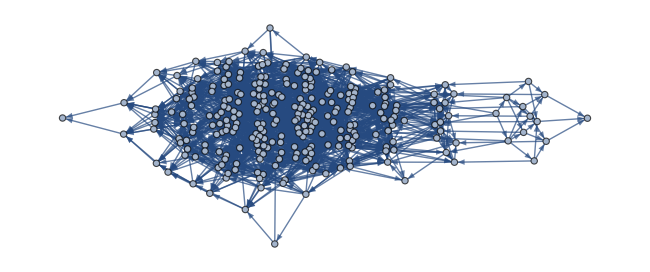

```mathematica
Graph[edges]
```

```mathematica
Map[{VertexList[#],EdgeList[#],#}&,{allGraphs5[26731,"graph"]}]
```

{{{1,2,3,4},{1<->2,3<->4},-Graphics-}}

```mathematica
allGraphs5[26731,"vertexsets"]/.{1->2}
```

{{2},{2,3},{4},{5}}

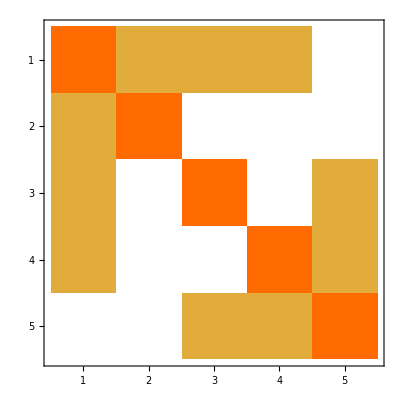
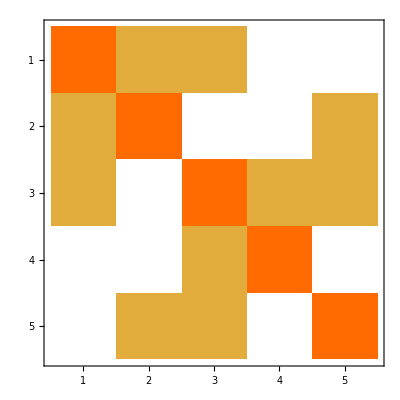
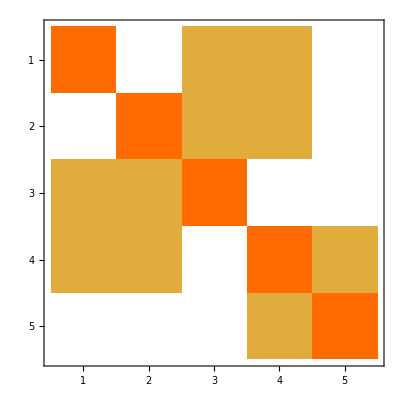

```mathematica
Table[allGraphs5[k,"matrix"]//MatrixPlot,{k,{28435,26283,9073}}]
```

```mathematica
Table[Indexed[x,{i,j}],{i,5},{j,5}]//MatrixForm
```

(x11 | x12 | x13 | x14 | x15
x21 | x22 | x23 | x24 | x25
x31 | x32 | x33 | x34 | x35
x41 | x42 | x43 | x44 | x45
x51 | x52 | x53 | x54 | x55)

```mathematica
MatrixForm[Table[Indexed[x,{i,j}],{i,5},{j,5}]/.First[Solve[allGraphs5[28435,"matrix"].Table[Indexed[x,{i,j}],{i,5},{j,5}]==allGraphs5[26283,"matrix"],Flatten[Table[Indexed[x,{i,j}],{i,5},{j,5}]]]]]
```

(-1 | -2 | 2 | 6 | -1
1 | 2 | -1 | -3 | 1
7/4 | 3/2 | -3/4 | -19/4 | 3/4
5/4 | 3/2 | -5/4 | -17/4 | 1/4
-3/2 | -1 | 3/2 | 9/2 | 1/2)

```mathematica
MatrixForm[Table[Indexed[x,{i,j}],{i,5},{j,5}]/.First[Solve[allGraphs5[28435,"matrix"].Table[Indexed[x,{i,j}],{i,5},{j,5}]==allGraphs5[9073,"matrix"],Flatten[Table[Indexed[x,{i,j}],{i,5},{j,5}]]]]]
```

(0 | 6 | 3 | 1 | -2
0 | -2 | -1 | 0 | 1
1 | -5 | -3/2 | -1 | 5/4
1 | -5 | -5/2 | 0 | 7/4
-1 | 5 | 2 | 1 | -1/2)

```mathematica
Table[
Table[ShowGraph5Least[k],{k,group}],{group,RandomSample[groups,5]}]//TableForm
```

-Graphics-269834 | -Graphics-221234 | -Graphics-207374 | -Graphics-206674 | -Graphics-10094 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-296472 | -Graphics-291742 | -Graphics-291822 | -Graphics-299292 | -Graphics-287772 | -Graphics-290082 | -Graphics-275792 | -Graphics-279842 | -Graphics-265012 | -Graphics-229522 | -Graphics-236802 | -Graphics-207812 | -Graphics-491952 | -Graphics-484482 | -Graphics-469382 | -Graphics-401352 | -Graphics-32812 | -Graphics-39792 | -Graphics-11022 | -Graphics-13362
-Graphics-319840 | -Graphics-361940 | -Graphics-368980 | -Graphics-383080 | -Graphics-514780 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-272982 | -Graphics-270102 | -Graphics-221262 | -Graphics-207482 | -Graphics-31962 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics-1971016 | -Graphics-680416 | -Graphics-291616 | -Graphics-9016 | -Graphics-416 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Tally[Map[Length,groups]]
```

{{1,5},{5,228},{20,24},{10,12},{15,10}}

```mathematica
Tally[Table[allGraphs5[k,"atleast"],{k,Keys[allGraphs5]}]]
```

{{34,1},{21,5},{16,15},{12,25},{8,70},{4,205},{2,375},{1,286},{0,201},{3,251},{6,180},{7,35},{5,106},{10,55},{11,10},{9,35},{15,15},{13,15},{24,5},{18,5}}

```mathematica
Table[
Table[ShowGraph5Least[k],{k,group}],{group,Select[groups,Length[#]==12&]}]//TableForm
```

{}

```mathematica
Table[
Table[ShowGraph5Least[k],{k,group}],{group,Select[groups,Length[#]==1&]}]//TableForm
```

-Graphics-034
-Graphics-295240
-Graphics-206653
-Graphics-590481
-Graphics-88595

```mathematica
Select[groups,Length[#]==1&]
```

{{0},{29524},{20665},{59048},{8859}}

```mathematica
Table[ShowGraph5Least[k],{k,quads}]
```

{-Graphics-360850,-Graphics-296050,-Graphics-295270,-Graphics-317110,-Graphics-295510}

```mathematica
Table[ShowGraph5Least[k],{k,alfa1s}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140}